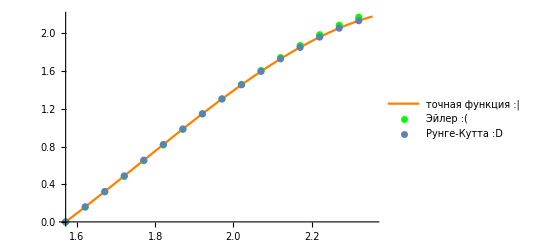

|  x |  y
 |  1.57080 |      0
 |  1.62080 |  0.15938
 |  1.67080 |  0.32254
 |  1.72080 |  0.48819
 |  1.77080 |  0.65500
 |  1.82080 |  0.82154
 |  1.87080 |  0.98636
 |  1.92080 |  1.14800
 |  1.97080 |  1.30480
 |  2.02080 |  1.45530
 |  2.07080 |  1.59790
 |  2.12080 |  1.73090
 |  2.17080 |  1.85280
 |  2.22080 |  1.96200
 |  2.27080 |  2.05670
 |  2.32080 |  2.13560

|  x |  y
 |  1.5708 |  0
 |  1.6208 |  0.15708
 |  1.6708 |  0.318564
 |  1.7208 |  0.48321
 |  1.7708 |  0.649706
 |  1.8208 |  0.816671
 |  1.8708 |  0.982664
 |  1.9208 |  1.14619
 |  1.9708 |  1.3057
 |  2.0208 |  1.45962
 |  2.0708 |  1.60633
 |  2.1208 |  1.74418
 |  2.1708 |  1.87152
 |  2.2208 |  1.98666
 |  2.2708 |  2.08794
 |  2.3208 |  2.17369

```mathematica
f[x_,y_]:=2x*Sin[x]+y*Cot[x];
a =0.5Pi;
b=0.75Pi;
precise[x_]:=(x^2-0.25 Pi^2)Sin[x];
precisePlot:=Plot[precise[x], {x,a,b},PlotStyle->Orange,PlotLegends->{"точная функция :|"}];
y0=0;x0=a;h=0.05;
m=Floor[(b-a)/h]+1;
rk4[f_,x0_,y0_,h_,m_]:=Block[{k1,k2,k3,k4,x=x0,y=y0,t,k},
k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];
k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];
k4[x_,y_]:=h*f[x+h,y+k3[x,y]];
t=Table[{x,y}={x+h,y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6},{k,m-1}];
t=Prepend[t,{x0,y0}];
Return[t]]
tab1:=rk4[f,x0,y0,h,m]
gr3=ListPlot[tab1, PlotLegends->{"Рунге-Кутта :D"}];
lst={{},{" x", " y"}};
x=x0;y=y0;
eul=Table[{x,y}={x+h,y+h*f[x,y]},{i,m-1}];
eul=Prepend[eul,{x0,y0}];
eiler=ListPlot[eul,PlotStyle->Green, PlotLegends->{"Эйлер :("}];
Show[{precisePlot, eiler,gr3}]
PaddedForm[TableForm[tab1,TableHeadings->lst],{5,5}]
PaddedForm[TableForm[eul,TableHeadings->lst,{5,5}]]
```